# Potential Folding

U=∫ρ[r]V[r]ⅆr
where ρ[r] is the density of charge, V[r] is the potential of each charge

```mathematica
(* woods-Saxon density *)
ρWS[r_,r0_,a_]:=1/(1+Exp[(r-r0)/a])
```

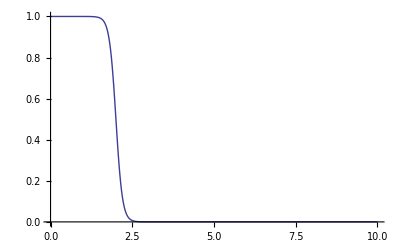

```mathematica
Plot[ρWS[r,2,0.1],{r,0,10}]
```

```mathematica
(* Yukawa potential *)
VY[r_,m_,g_]:=-g^2 Exp[-m r]/r
```

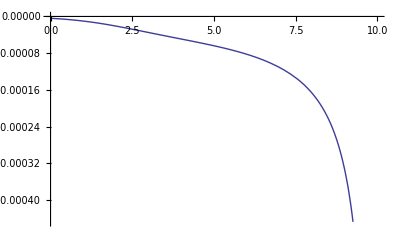

```mathematica
Plot[ρWS[r,2,1]VY[10-r,1,1],{r,0,10}]
```

```mathematica
(* force *)
D[VY[r,m,g],r]//Simplify
```

(ⅇ^(-m r) g^2 (1+m r))/r^2

```mathematica
(* 1D folding *)
Integrate[ρWS[r,2,0.1]VY[R-r,1,1],{r,0,4},Assumptions->R>8]
```

Integrate[-ⅇ^(r-R)/((1+ⅇ^(10. (-2+r))) (-r+R)),{r,0,4},Assumptions→R>8]